```mathematica
AA[n_,k_] :=(-1)^(k+1)/((k-1)!)Integrate[ t^(k-1)E^(-t),{t,-Log[n],0}]
```

```mathematica
AA[n,4]
```

1/6 (6-6 n+6 n Log[n]-3 n Log[n]^2+n Log[n]^3)

```mathematica
BB[n_,k_] := ((-1)^(1+k) (-Gamma[k]+Gamma[k,-Log[n]]))/((-1+k)!)
```

```mathematica
N[Re[BB[100,3]]]
```

698.863

```mathematica
N[Re[AA[100,2.5]]]
```

-532.148

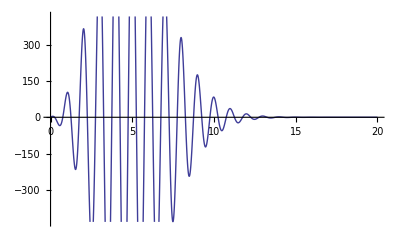

```mathematica
Plot[Re[BB[100,k]],{k,0,20}]
```

```mathematica
DD[ k_, a_, n_ ] := Sum[ Binomial[k,j] DD[ k-j, m+1, Floor[n/(m^j)]], {m,a, n^(1/k)},{j,1,k}]
```

```mathematica
DD[ 1,a_, n_ ]:= Floor[n]-a+1
DD[0,a_,n_] := 1
DS[ n_, k_ ] := DD[k,2,n]
```

```mathematica
DDD[n_, k_ ] := Sum[ DDD[n/j, k-1],{j,2,n}]
```

```mathematica
DDD[n_,0] := 1
```

```mathematica
DDD[1000,4]
```

13952

```mathematica
DS[1000,4]
```

13952

```mathematica
N[Re[BB[1000,4]]]
```

36986.5

```mathematica
Sum[N[(-1)^k  Re[ BB[1000,k]]],{k,1,100}]
```

-6.90776

```mathematica
Log[100.]
```

4.60517

```mathematica
N[Sum[(-1)^k  BB[100,k],{k,1,Infinity}]]
```

-4.60517

```mathematica
FullSimplify[Expand[(-1)^4 BB[n,4]]]
```

1-1/6 Gamma[4,-Log[n]]

```mathematica
MM[ n_ ] := N[Log[n] + Sum[(-1)^k  BB[n,k],{k,1,1000}]]
```

```mathematica
MM[25]
```

-2.0373×10^-11-4.21325×10^-15 ⅈ

```mathematica
MR[ n_ ]:= Table[ (-1)^j ( N[Re[BB[n,j]- DS[n,j]]]),{j,1,40}]
```

```mathematica
MR[1000]
```

{0.,838.755,-6732.79,23034.5,-47283.1,68136.9,-76237.1,70959.4,-57374.1,41305.1,-26867.,15943.6,-8700.17,4394.66,-2066.48,908.988,-375.623,146.364,-53.956,18.8735,-6.28092,1.99339,-0.60465,0.175638,-0.0489469,0.0131083,-0.0033787,0.000839374,-0.00020125,0.0000466253,-0.00001045,2.26818×10^-6,-4.77251×10^-7,9.74388×10^-8,-1.93205×10^-8,3.72366×10^-9,-6.98111×10^-10,1.2744×10^-10,-2.26507×10^-11,3.93932×10^-12}

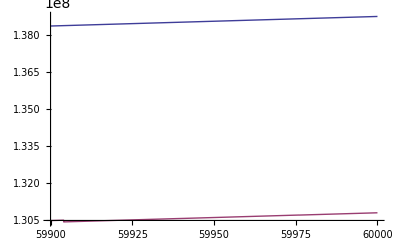

```mathematica
Plot[ {BB[n,8], BB[n,8]-DS[n,8]},{n,59900,60000}]
```

```mathematica
DS[n,k]
```

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of $IterationLimit :: itlim will be suppressed during this calculation.

```mathematica
D2[1,a_,n_,p_,r_] := n-a+1
D2[2,a_,n_,p_,r_] := p/((r+1)(r+2)) + (Floor[n/a]-a)(p/(r+1))+(Floor[n^(1/2)]-a)(p/2) + p Sum[ Floor[n/m] - m,{m,a+1, n^(1/2)}]
```

```mathematica
D2[k_, a_,n_,p_,r_] := D2[k-1, a, n/a, p/(r+1), r+1] + Sum[ D2[ k-1, m, n/m, p, 1 ], {m,a+1, n^(1/k)}]
```

```mathematica
DD2[ n_, k_] := D2[ k, 2, n, k!, 0 ]
```

```mathematica
DDM[ n_] := Sum[ (-1)^k DD2[n,k],{k,1,Log[n]/Log[2]}]
```

```mathematica
DDM[100]
```

0

```mathematica
D3[1,a_,n_,p_,r_] := n-a+1
D3[2,a_,n_,p_,r_] := p/((r+1)(r+2)) + (n/a-.5-a)(p/(r+1))+(n^(1/2)-.5-a)(p/2) + p Sum[n/m-.5 - m,{m,a+1, n^(1/2)}]
```

```mathematica
D3[k_, a_,n_,p_,r_] := D3[k-1, a, n/a, p/(r+1), r+1] + Sum[ D3[ k-1, m, n/m, p, 1 ], {m,a+1, n^(1/k)}]
```

```mathematica
DD3[ n_, k_] := D3[ k, 2, n, k!, 0 ]
```

```mathematica
DDM3[ n_] := Sum[ (-1)^k DD3[n,k],{k,1,Log[n]/Log[2]}]
```

```mathematica
DDM3[1000.]
```

4.56758

Sum::itflrw: Warning: In evaluating Floor[Log[4]/Log[2]] to find the number of iterations to use for Sum, $MaxExtraPrecision = 50. was encountered. An upper estimate will be used for the number of iterations.

Sum::itflrw: Warning: In evaluating Floor[Log[8]/Log[2]] to find the number of iterations to use for Sum, $MaxExtraPrecision = 50. was encountered. An upper estimate will be used for the number of iterations.

Sum::itflrw: Warning: In evaluating Floor[Log[16]/Log[2]] to find the number of iterations to use for Sum, $MaxExtraPrecision = 50. was encountered. An upper estimate will be used for the number of iterations.

General::stop: Further output of Sum :: itflrw will be suppressed during this calculation.

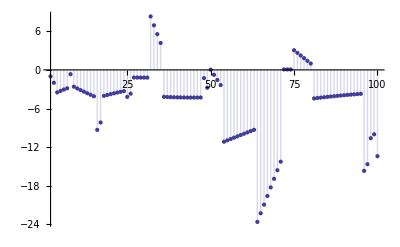

```mathematica
DiscretePlot[DDM3[n],{n,2,100}]
```

```mathematica
DD3[ 1001, 4]
```

13952

```mathematica
DS[1000,4]
```

13952

```mathematica
FullSimplify[DD2[n,2]]
```

-5+Floor[√n]+2 Floor[n/2]+2 ∑_(m=3)^(√n) (-m+Floor[n/m])

```mathematica
DD2[n,3]
```

$Aborted

```mathematica
D2[2, 2, n/2, (3!)/(0+1), 0+1] + Sum[ D2[2, m, n/m, 3!, 1 ], {m,2+1, n^(1/3)}]
```

$Aborted

```mathematica
FullSimplify[ 2 ∑_(m=3)^(√n) (-m )+2 ∑_(m=3)^(√n) (Floor[n/m] )]
```

```mathematica
FullSimplify[-5+Floor[√n]+2 Floor[n/2]+6-√n-n+2 ∑_(m=3)^(√n) Floor[n/m]]
```

1-√n-n+Floor[√n]+2 Floor[n/2]+2 ∑_(m=3)^(√n) Floor[n/m]

```mathematica
EE[n_] :=EE[n]= -Log[n]- Sum[ EE[n/j],{j,2,n}]
```

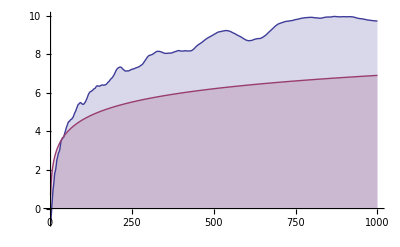

```mathematica
DiscretePlot[{EE[n], Log[n]},{n,2,1000}]
```

```mathematica
Clear[FF]
```

```mathematica
FF[n_,k_] :=Sum[j(1/k-FF[n/j,k+1]),{j,2,n}]
FG[n_,k_] :=Sum[1/k-FG[n/j,k+1],{j,2,n}]
FH[n_] :=Sum[Log[j]-FH[n/j],{j,2,n}]
```

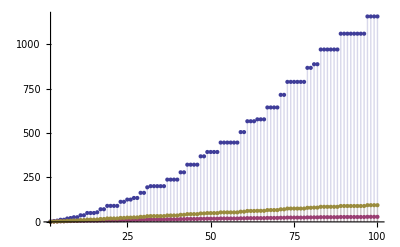

```mathematica
DiscretePlot[{FF[n,1],FG[n,1],FH[n]},{n,2,100}]
```

```mathematica
FR[n_,k_,j_] :=1/k-FR[n/j,k+1, 2] + FR[n,k,j+1]
```

```mathematica
FQ[n_,k_,j_] :=If[j<n,1/k-FQ[n/j,k+1, 2] + FQ[n,k,j+1],0]
```

```mathematica
FQ[100,1,2]
```

428/15

```mathematica
FS[n_,j_] :=If[j<n,Log[j]-FS[n/j,2] + FS[n,j+1],0]
```

```mathematica
N[FS[100,2]]
```

94.0453

```mathematica
N[FH[100]]
```

94.0453

```mathematica
FS[n,2]
```

If[2<n,Log[2]-FS[n/2,2]+FS[n,2+1],0]

```mathematica
FullSimplify[FQ[n,1,2]]
```

If[n>2,1 1/1-FQ[n/2,1+1,2]+FQ[n,1,2+1],0]

```mathematica
PP[n_,j_] := Piecewise[{{Log[j]-PP[n/j,2] + PP[n,j+1],n>j},{0,n≤ j}}]
```

```mathematica
N[PP[100,2]]
```

94.0453

```mathematica
PP[n,2]
```

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of $IterationLimit :: itlim will be suppressed during this calculation.

$Aborted